# Classifying Cellular Automata by Compression

## Ben Jacobsohn

## Introduction

Cellular Automata are a class of system that sequentially updates cells based on the configuration of some of the previous generation’s cells and starting from some specified initial condition. There are many possible rules to determine the updates, and they can produce drastically different behavior. In Wolfram’s New Kind of Science (and before), he classifies these rules based on the types of behavior they produce as follows:

Class 1: The simplest behavior, quickly becomes uniform from almost all initial conditions
Class 2: Settles to simple repetition or persistent structures
Class 3: Seemingly random behavior with localized structures
Class 4: Localized structures that interact in complex ways

	In 2009, Hector Zenil authored a paper classifying cellular automata by clustering them based on the amount of lossless compression that could be done on their final states. In general, class 1 automata will exhibit the most repetition, followed by class 2, class 4, and finally class 3. Lossless compression is necessarily related to the amount of repetition in a file, so the amount of compression possible for each class should follow this same ordering. Shown below are examples of each class of behavior with three-color totalistic cellular automata from random initial conditions, along with the ratio of their uncompressed to compressed file sizes.

```mathematica
size=250;
cellGrid[rule_] := CellularAutomaton[{rule, {3, 1}}, RandomInteger[1, size], size]
compressionRatio[cells_] := N[ByteCount[cells]/ByteCount[Compress[cells]], 4]
```

```mathematica
Text[Row[Column[cells=cellGrid[#[[1]]];{ArrayPlot[cells,ImageSize->Small],"Rule "<>ToString[#[[1]]],"Ratio "<>ToString[compressionRatio[cells]],"Class "<>#[[2]]}]&/@{{1011,"1"},{1032,"2"},{1068,"3"},{1041,"4"}}]]
```

-Graphics-
Rule 1011
Ratio 279.0
Class 1-Graphics-
Rule 1032
Ratio 97.92
Class 2-Graphics-
Rule 1068
Ratio 17.51
Class 3-Graphics-
Rule 1041
Ratio 40.84
Class 4

The compression ratios are in the order stated above. The gap between the ratios of automata from classes 3 and 4 is much smaller than that between classes 1 and 2, but is still readily apparent. Automata could be classified relatively easily with this scheme, but here the focus is on sensitivity to initial conditions.

## Testing

Instead of looking at the overall compression behavior of the automata, we can examine how the compression changes cumulatively row by row in each automata. This shows how the evolving states of the automata are related to their respective initial conditions. Here, five examples of automata from each class are analyzed in this manner and their relative compression between rows are plotted along with the others of their respective class.

```mathematica
compressByRow[cells_]:=compressionRatio/@cells
```

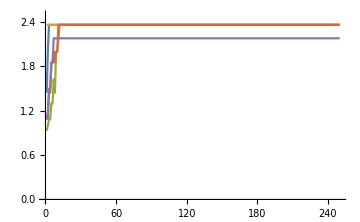
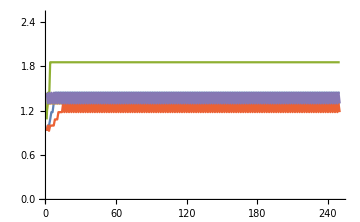
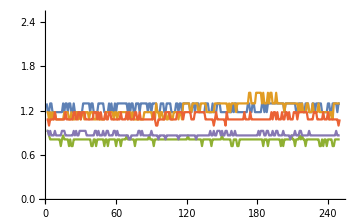
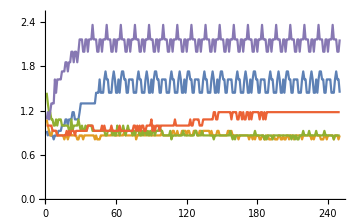
-Graphics-
Class 1-Graphics-
Class 2-Graphics-
Class 3-Graphics-
Class 4

```mathematica
classes = {{1011, 1012, 1014, 1015, 1016},
   {1005, 1008, 1032, 1047, 1050},
   {1000, 1001, 1017, 1003, 1020},
   {1035, 1038, 1039, 1042, 1043}};

Row[Table[Column[{ListLinePlot[Table[
FoldList[Times, Ratios[compressByRow[cellGrid[r]]]], 
{r, classes[[i]]}],ImageSize->Medium,PlotRange->2.5],Text["Class "<>ToString[i]]}], {i, 4}]]
```

## Conclusions

Class 1 automata increase in compression quickly compared to their random initial rows, then level off as essentially all information from the initial condition is lost as the automata becomes uniform. 
	In class 2 automata, the compression either fluctuates for simple periodic behavior, or compressed greatly and becomes constant or relatively constant as persistent local structures are formed. 
	Class 3 shows the  least compressibility, as each row evolves seemingly randomly with only small localized structures depending on the specific rule. 
	Class 4 automata showed the most variability in compression based on the specific rule, depending on the sizes and interactions of the localized structures produced. They then reach a point of relative stability or simple repetition as the structures produced from the rule develop more and depend more on the general behavior of the rule than the local structures produced from the initial condition.
	This is ultimately pretty useless, but serves as an interesting analysis and visualization of how cellular automata from different classes evolve over time depending on their initial conditions.